Front→Back
Right→Left
Up→Down
Back→Front
Left→Right
Down→Up

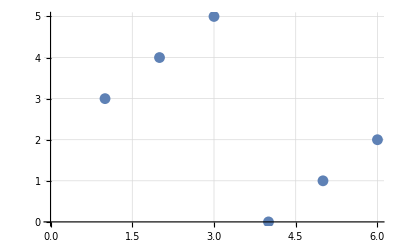

```mathematica
ns={Front,Right,Up,Back,Left,Down};
f[i_]:=Mod[(i+3),6];
at[i_,list_]:=list[[i+1]];
Table[at[i,ns]->at[f[i],ns],{i,0,Length[ns]-1}]//Column
ListPlot[Table[Mod[(i+3),6],{i,0,5}],GridLines->Automatic]
```